## Funkcijske vrste

## Fourierova vrsta

Za razvoj funkcij v trigonometrične vrste ima Mathematica vgrajene funkcije.

```mathematica
?FourierSeries
?FourierTrigSeries
?FourierSinSeries
?FourierCosSeries
```

Vse funkcije privzemajo, da funkcije razvijamo na intervalu (-π,π). Razvoj na intervalu (-T/2,T/2) dobimo tako, da v ukaz dodamo opcijo FourierParameters→{1,(2π)/T}.

Funkcijo zlepljeno iz dveh formul se da zapisati z ukazom If[], Which[] ali Piecewise[].

1. Funkcijo f(x)=x+(2x)/(|x|)razvijte v Fourierjevo vrsto na intervalu (-3,3) do členov z indeksi n=12.
Skicirajte graf funkcije in graf Fourierjevega približka na intervalu (-6,6).

-(7 ⅈ ⅇ^(-1/3 ⅈ π x))/π+(7 ⅈ ⅇ^((ⅈ π x)/3))/π-(3 ⅈ ⅇ^(-2/3 ⅈ π x))/(2 π)+(3 ⅈ ⅇ^((2 ⅈ π x)/3))/(2 π)-(7 ⅈ ⅇ^(-ⅈ π x))/(3 π)+(7 ⅈ ⅇ^(ⅈ π x))/(3 π)-(3 ⅈ ⅇ^(-4/3 ⅈ π x))/(4 π)+(3 ⅈ ⅇ^((4 ⅈ π x)/3))/(4 π)-(7 ⅈ ⅇ^(-5/3 ⅈ π x))/(5 π)+(7 ⅈ ⅇ^((5 ⅈ π x)/3))/(5 π)-(ⅈ ⅇ^(-2 ⅈ π x))/(2 π)+(ⅈ ⅇ^(2 ⅈ π x))/(2 π)-(ⅈ ⅇ^(-7/3 ⅈ π x))/π+(ⅈ ⅇ^((7 ⅈ π x)/3))/π-(3 ⅈ ⅇ^(-8/3 ⅈ π x))/(8 π)+(3 ⅈ ⅇ^((8 ⅈ π x)/3))/(8 π)-(7 ⅈ ⅇ^(-3 ⅈ π x))/(9 π)+(7 ⅈ ⅇ^(3 ⅈ π x))/(9 π)-(3 ⅈ ⅇ^(-10/3 ⅈ π x))/(10 π)+(3 ⅈ ⅇ^((10 ⅈ π x)/3))/(10 π)-(7 ⅈ ⅇ^(-11/3 ⅈ π x))/(11 π)+(7 ⅈ ⅇ^((11 ⅈ π x)/3))/(11 π)-(ⅈ ⅇ^(-4 ⅈ π x))/(4 π)+(ⅈ ⅇ^(4 ⅈ π x))/(4 π)

-(14 Sin[(π x)/3])/π-(3 Sin[(2 π x)/3])/π-(14 Sin[π x])/(3 π)-(3 Sin[(4 π x)/3])/(2 π)-(14 Sin[(5 π x)/3])/(5 π)-Sin[2 π x]/π-(2 Sin[(7 π x)/3])/π-(3 Sin[(8 π x)/3])/(4 π)-(14 Sin[3 π x])/(9 π)-(3 Sin[(10 π x)/3])/(5 π)-(14 Sin[(11 π x)/3])/(11 π)-Sin[4 π x]/(2 π)

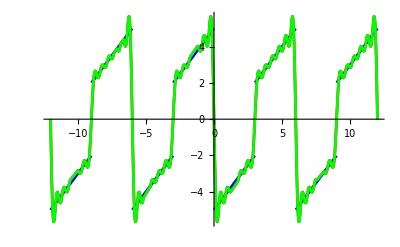

```mathematica
Clear[f, ff, x, fF, fTF];
ff[x_] = x + 2x/Abs[x];
T = 6;
f[x_] = ff[Mod[x,T]-T/2]; 
fF =FourierSeries[f[x],x, 12, FourierParameters->{1, 2Pi/T}]
fTF =FourierTrigSeries[f[x],x, 12, FourierParameters->{1, 2Pi/T}]

Plot[{f[x], fF, fTF}, {x, -2T, 2T}, PlotStyle->{Blue, Red, Green}]
```

2. Funkcijo    f(x)={   0 ,  -π<x<0
x ,     0<x<π
razvijte v
  a.  Fourierovo  vrsto na intervalu  (-π,π)
b.  sinusno Fourierovo  vrsto na intervalu  (0,π)
c.  kosinusno Fourierovo  vrsto na intervalu  (0,π)

Narišite grafe delnih vsot vrst (upoštevajte indekse do n=10) na intervalu (-π,π) in primerjajte grafe z grafom funkcije  y=f(x).

π/4-(2 Cos[x])/π-(2 Cos[3 x])/(9 π)-(2 Cos[5 x])/(25 π)-(2 Cos[7 x])/(49 π)-(2 Cos[9 x])/(81 π)+Sin[x]-1/2 Sin[2 x]+1/3 Sin[3 x]-1/4 Sin[4 x]+1/5 Sin[5 x]-1/6 Sin[6 x]+1/7 Sin[7 x]-1/8 Sin[8 x]+1/9 Sin[9 x]-1/10 Sin[10 x]

-2 (-Sin[x]+1/2 Sin[2 x]-1/3 Sin[3 x]+1/4 Sin[4 x]-1/5 Sin[5 x]+1/6 Sin[6 x]-1/7 Sin[7 x]+1/8 Sin[8 x]-1/9 Sin[9 x]+1/10 Sin[10 x])

π/2-(4 Cos[x])/π-(4 Cos[3 x])/(9 π)-(4 Cos[5 x])/(25 π)-(4 Cos[7 x])/(49 π)-(4 Cos[9 x])/(81 π)

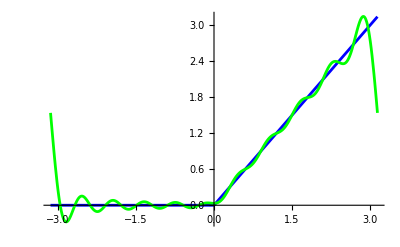

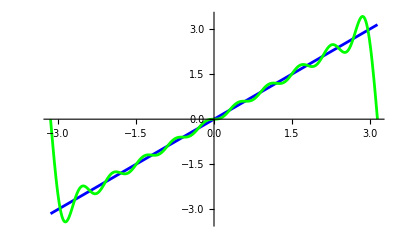

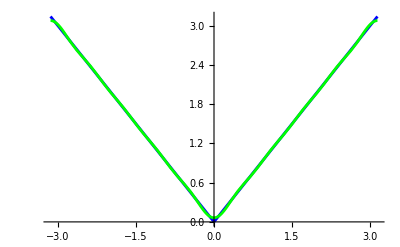

```mathematica
Clear[x];
f = Piecewise[{{0, -Pi<=x<=0}, {x, 0<x<=Pi}}];

fb = x;
fc = Piecewise[{{-x, -Pi<=x<=0},{x, 0<x<=Pi}}];
a = FourierTrigSeries[f, x, 10]
b = FourierSinSeries[fb, x, 10]
c = FourierCosSeries[fc, x, 10]

Plot[{f,a},{x, -Pi, Pi}, PlotStyle->{Blue, Green}]
Plot[{fb,b},{x, -Pi, Pi}, PlotStyle->{Blue, Green}]
Plot[{fc,c},{x, -Pi, Pi}, PlotStyle->{Blue, Green}]
```

3. Funkcijo f(x)=sin(x), ki je podana na intervalu (0,π),sodo nadaljujte na interval (-π,0) ter tako dobljeno funkcijo razvijte v kosinusno Fourierovo vrsto na intervalu (-π,π).
Rezultat: f(x)=2/π-(∑^∞)_(k=1)4/((2k-1)(2k+1)π)cos(2k x).

Abs[Sin[x]]

2/π-(4 Cos[2 x])/(3 π)-(4 Cos[4 x])/(15 π)-(4 Cos[6 x])/(35 π)-(4 Cos[8 x])/(63 π)-(4 Cos[10 x])/(99 π)

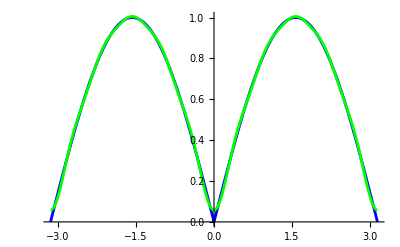

```mathematica
Clear[x];
f = Abs[Sin[x]]
fc = FourierCosSeries[f, x, 10]

Plot[{f, fc},{x, -Pi, Pi}, PlotStyle->{Blue, Green}]
```

4. V datoteki ekg.txt so shranjeni podatki srčnega utripa (EKG meri napetost v mV), prvi podatek je časovni korak (v sekundah).
(a) Iz podatkov izluščite le podatke za vsako stotinko za nekaj utripov in jih izrišite z ukazom ListPlot.
(b) Iz teh podatkov sestavite funkcijo f(x) z ukazom ListInterpolate.
(c) Razvijte funkcijo f(x) v Furierovo vrsto, pri čemer upoštevajte 50 členov (konstantni člen ter 50 sinusov in 50 kosinusov). Uporabite ukaz za numeričen izračun Fourierove vrste NFourierTrigSeries, ki je del paketa FourierSeries`.
(d) Na istem grafu izrišite utrip in Fourierovo vrsto. Izrišite tudi graf napake.

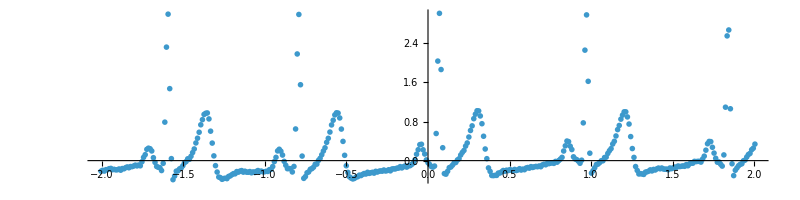

```mathematica
Clear[utrip,dt,l,time,m,M,f,perioda,podatki]
(* nalozimo datoteko s podatki *)
utrip=Import[StringJoin[NotebookDirectory[],"ekg.txt"],"List"]
(* preberemo časovni korak in količino podatkov *)
dt=First[utrip];
l=Length[utrip];
(* iz podatkov izberemo le podatke za vsako stotinko na nekem segmentu (nekaj utripov) *)
utrip=Take[utrip,{1501,5501,10}];
(* popravimo časovni korak in izračunamo celoten čas *)
dt=dt*10;
l=Length[utrip];
time=l*dt;
(* izrišemo podatke na simetričen interval *)
podatki=ListPlot[utrip,DataRange->{-time/2,time/2},AspectRatio->1/4,PlotRange->All,PlotStyle->PointSize[0.005],ImageSize->800]
```

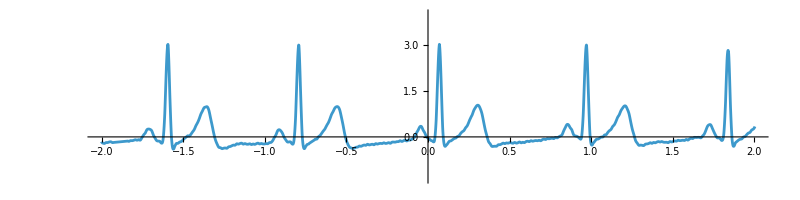

```mathematica
(* razberemo razpon vrednosti v podatkih - minumum in maksimum *)
M=Max[utrip]+1;
m=Min[utrip]-1;
(* iz diskretnih podatkov sestavimo zvezno funkcijo (interpolacija), za definicijsko območje izberemo isti interval kot prej *)
f=ListInterpolation[utrip,{{-time/2,time/2}}];
(* narišemo utrip *)
Plot[f[x],{x,-time/2,time/2},AspectRatio->1/4,PlotRange->{m,M},ImageSize->800]
```

```mathematica
(* določimo dolzino periode (enega utripa) *)
FindPeaks[utrip,0,0,2.8] (* poišče vrhove v podatkih, ki so večji od 2.8 *)
perioda=(%[[3,1]]-%[[2,1]])*dt
(* nalozimo paket za numeričen izračun Fourierove vrste in izračunamo Fourierovo vrsto *)
Needs["FourierSeries`"]
fourier=NFourierTrigSeries[f[x],x,50,FourierParameters->{1,2π/perioda}]//Simplify
```

{{42,2.999},{122,2.993},{208,3.016},{298,2.984}}

0.86

0.0976723+0.154931 Cos[7.30603 x]+0.00603819 Cos[14.6121 x]+0.236984 Cos[21.9181 x]-0.160815 Cos[29.2241 x]-0.139053 Cos[36.5301 x]-0.151989 Cos[43.8362 x]-0.228192 Cos[51.1422 x]-0.10391 Cos[58.4482 x]-0.0507514 Cos[65.7543 x]+0.0345267 Cos[73.0603 x]+0.10582 Cos[80.3663 x]+0.124151 Cos[87.6724 x]+0.117519 Cos[94.9784 x]+0.074445 Cos[102.284 x]+0.0204086 Cos[109.59 x]-0.0232103 Cos[116.896 x]-0.0577034 Cos[124.203 x]-0.06801 Cos[131.509 x]-0.0589751 Cos[138.815 x]-0.035781 Cos[146.121 x]-0.0109399 Cos[153.427 x]+0.00857661 Cos[160.733 x]+0.0218162 Cos[168.039 x]+0.0261241 Cos[175.345 x]+0.0212564 Cos[182.651 x]+0.0125639 Cos[189.957 x]+0.00224018 Cos[197.263 x]-0.0037139 Cos[204.569 x]-0.00727098 Cos[211.875 x]-0.00701525 Cos[219.181 x]-0.00611749 Cos[226.487 x]-0.00259394 Cos[233.793 x]+0.0000520942 Cos[241.099 x]+0.00212976 Cos[248.405 x]+0.00273598 Cos[255.711 x]+0.00265497 Cos[263.017 x]+0.00155393 Cos[270.323 x]+0.000899758 Cos[277.629 x]-0.00030568 Cos[284.935 x]-0.000185573 Cos[292.241 x]-0.000814704 Cos[299.547 x]-0.00103375 Cos[306.853 x]-0.0000706503 Cos[314.159 x]-0.0010864 Cos[321.465 x]-0.000394018 Cos[328.771 x]-0.000205281 Cos[336.077 x]-0.0000413709 Cos[343.383 x]+0.000542627 Cos[350.689 x]+0.000809068 Cos[357.995 x]+0.00109267 Cos[365.301 x]+0.326961 Sin[7.30603 x]-0.102318 Sin[14.6121 x]+0.15204 Sin[21.9181 x]+0.218269 Sin[29.2241 x]-0.0189627 Sin[36.5301 x]+0.0465175 Sin[43.8362 x]-0.0943435 Sin[51.1422 x]-0.158588 Sin[58.4482 x]-0.146303 Sin[65.7543 x]-0.155813 Sin[73.0603 x]-0.0838784 Sin[80.3663 x]-0.0203397 Sin[87.6724 x]+0.045877 Sin[94.9784 x]+0.0911935 Sin[102.284 x]+0.10326 Sin[109.59 x]+0.0883561 Sin[116.896 x]+0.0582272 Sin[124.203 x]+0.0174435 Sin[131.509 x]-0.0158476 Sin[138.815 x]-0.039573 Sin[146.121 x]-0.0426157 Sin[153.427 x]-0.0371305 Sin[160.733 x]-0.0224257 Sin[168.039 x]-0.00768717 Sin[175.345 x]+0.00293296 Sin[182.651 x]+0.00978645 Sin[189.957 x]+0.0146948 Sin[197.263 x]+0.0115506 Sin[204.569 x]+0.00618165 Sin[211.875 x]+0.00149889 Sin[219.181 x]-0.00168377 Sin[226.487 x]-0.00305078 Sin[233.793 x]-0.00571347 Sin[241.099 x]+0.00387583 Sin[248.405 x]+0.00214481 Sin[255.711 x]-0.00141541 Sin[263.017 x]+0.00203879 Sin[270.323 x]+0.000170725 Sin[277.629 x]+0.00308981 Sin[284.935 x]+0.000325446 Sin[292.241 x]+0.00173985 Sin[299.547 x]-0.000661471 Sin[306.853 x]+0.000627457 Sin[314.159 x]-0.000671669 Sin[321.465 x]-0.00039439 Sin[328.771 x]-0.00123406 Sin[336.077 x]-0.00100617 Sin[343.383 x]-0.000688539 Sin[350.689 x]-0.000285913 Sin[357.995 x]+0.000168639 Sin[365.301 x]

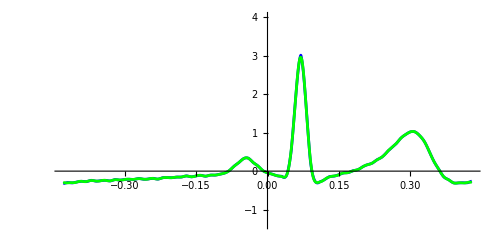

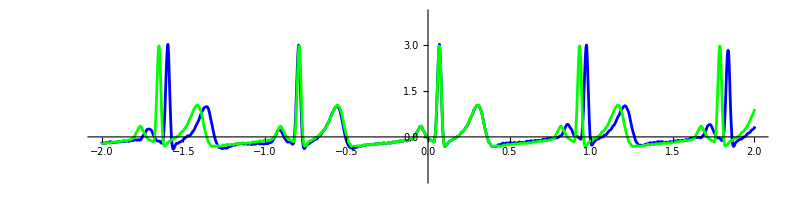

```mathematica
(* graf utripa in Fourierove vrste *)
Plot[{f[x],fourier},{x,-perioda/2,perioda/2},AspectRatio->1/2,PlotRange->{m,M},PlotStyle->{Blue,Green},ImageSize->500]
(* graf utripa in Fourierove vrste *)
Plot[{f[x],fourier},{x,-time/2,time/2},AspectRatio->1/4,PlotRange->{m,M},PlotStyle->{Blue,Green},ImageSize->800]
```

5. V datoteki zvok.txt so shranjeni podatki zvočnega signala (odmik tlaka od atmosferskega tlaka merjeno v Pa) za vsake 0.2 sekunde. Zvočni signal je mešanica zvoka več različnih harmonično usklajenih frekvenc. Ugotovite katere so te frekence in kakšne amplitude jim pripadajo na naslednji način:
(a) Izrišite zvočni signal na simetričnem intervalu in določite njegovo osnovno periodo.
(b) Iz podatkov sestavite funkcijo in jo razvijte v Fourierovo vrsto. Uporabite ukaz za numeričen izračun vrste in upoštevajte 15 členov razvoja.
(c) Določite vse frekvence, ki sestavljajo dani zvočni signal, in pripadajoče amplitude. Pomagajte si z ukazom Chop.
(d) Primerjajte grafa podatkov in Fourierove vrste, tako da jih prikažete na isti sliki.

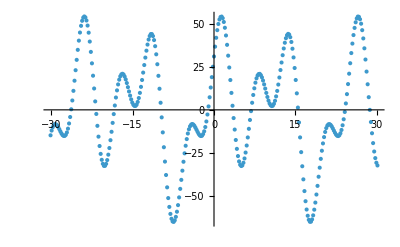

{{32,54.2386},{158,54.1757},{283,54.1723}}

25.2

```mathematica
Clear[zvok,dt,cas,perioda,z,Z,F]
zvok=Import[StringJoin[NotebookDirectory[],"zvok.txt"],"List"];
dt=0.2;
cas=Length[zvok]*dt;
ListPlot[zvok,DataRange->{-cas/2,cas/2}]
FindPeaks[zvok,0,0,50]
perioda=(%[[2,1]]-%[[1,1]])*dt
```

```mathematica
z=ListInterpolation[zvok,{{-cas/2,cas/2}}];
Needs["FourierSeries`"]
Z=NFourierTrigSeries[z[x],x,15,FourierParameters->{1,2π/perioda}]//Simplify
```

0.0073103+0.0507859 Cos[0.249333 x]+30.9915 Cos[0.498666 x]-0.0360335 Cos[0.747998 x]+0.0140518 Cos[0.997331 x]-0.00847376 Cos[1.24666 x]+0.00721667 Cos[1.496 x]-0.0040261 Cos[1.74533 x]-0.000994477 Cos[1.99466 x]-0.00286059 Cos[2.24399 x]+0.00434982 Cos[2.49333 x]+0.0000684298 Cos[2.74266 x]+0.00327298 Cos[2.99199 x]-0.0000951195 Cos[3.24133 x]+0.000218492 Cos[3.49066 x]-0.00154532 Cos[3.73999 x]+17.0103 Sin[0.249333 x]-0.0382801 Sin[0.498666 x]+0.0627206 Sin[0.747998 x]+25. Sin[0.997331 x]-0.068035 Sin[1.24666 x]+0.0347719 Sin[1.496 x]-0.0230768 Sin[1.74533 x]+0.0173996 Sin[1.99466 x]-0.0172093 Sin[2.24399 x]+0.0120156 Sin[2.49333 x]-0.0157476 Sin[2.74266 x]+0.0104783 Sin[2.99199 x]-0.00730579 Sin[3.24133 x]+0.0109217 Sin[3.49066 x]-0.0076054 Sin[3.73999 x]

```mathematica
F=Chop[Z,0.1]
```

```mathematica
Show[
Plot[F,{x,-cas/2,cas/2}],
ListPlot[zvok,DataRange->{-cas/2,cas/2},PlotStyle->Red]
]
```